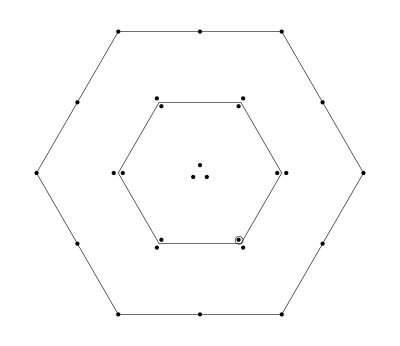

Y=-1.5,  I_3=0.5

(us+su)(ūd̄+d̄ū)+2ss(s̄d̄+d̄s̄)-3(sd+ds)d̄d̄

```mathematica
(*-------------------------------*)
```

The current J:

3 ((d̄)_b σ^αμ C((d̄)_a)^T-(d̄)_a σ^αμ C((d̄)_b)^T) (d_a^T C σ^αμ s_b)+3 ((d̄)_b σ^αμ C((d̄)_a)^T-(d̄)_a σ^αμ C((d̄)_b)^T) (s_a^T C σ^αμ d_b)+2 (s_a^T C σ^αμ s_b) ((d̄)_a σ^αμ C((s̄)_b)^T-(d̄)_b σ^αμ C((s̄)_a)^T)+2 (s_a^T C σ^αμ s_b) ((s̄)_a σ^αμ C((d̄)_b)^T-(s̄)_b σ^αμ C((d̄)_a)^T)+(s_a^T C σ^αμ u_b) ((d̄)_a σ^αμ C((ū)_b)^T-(d̄)_b σ^αμ C((ū)_a)^T)+(u_a^T C σ^αμ s_b) ((d̄)_a σ^αμ C((ū)_b)^T-(d̄)_b σ^αμ C((ū)_a)^T)+(s_a^T C σ^αμ u_b) ((ū)_a σ^αμ C((d̄)_b)^T-(ū)_b σ^αμ C((d̄)_a)^T)+(u_a^T C σ^αμ s_b) ((ū)_a σ^αμ C((d̄)_b)^T-(ū)_b σ^αμ C((d̄)_a)^T)

the Fierz rearranged J (to naively get the decay partten)

```mathematica
12 (d̄(γ̄)^5 s) (2 (s̄(γ̄)^5 s)-3 (d̄(γ̄)^5 d))-6 (d̄ σ^μν d d̄ σ^μν s)+4 (d̄ σ^μν s s̄ σ^μν s)+12 (d̄(γ̄)^5 s ū(γ̄)^5 u)+12 (d̄(γ̄)^5 u ū(γ̄)^5 s)+2 (d̄ σ^μν s ū σ^μν u)+2 (d̄ σ^μν u ū σ^μν s)+12 (d̄ 1s ū 1u)+12 (d̄ 1u ū 1s)+12 (d̄ 1s) (2 (s̄ 1s)-3 (d̄ 1d))
```

Π(q^2)=
-(3 log(-q^2/μ^2) q^8)/(64 π^6)-(5 ⟨ GG ⟩ log(-q^2/μ^2) q^4)/(8 π^5)-(33 ⟨ d̄ d⟩ log(-q^2/μ^2) m_d q^4)/(2 π^4)-(23 ⟨ s̄ s⟩ log(-q^2/μ^2) m_s q^4)/(2 π^4)-(2 ⟨ ū u⟩ log(-q^2/μ^2) m_u q^4)/π^4-(216 ⟨ d̄ d⟩^2 log(-q^2/μ^2) q^2)/π^2-(96 ⟨ s̄ s⟩^2 log(-q^2/μ^2) q^2)/π^2-(24 ⟨ ū u⟩^2 log(-q^2/μ^2) q^2)/π^2+(15 ⟨G^3⟩ log(-q^2/μ^2) q^2)/(8 π^6)+(288 ⟨ d̄ d⟩ ⟨ s̄ s⟩ log(-q^2/μ^2) q^2)/π^2+(144 ⟨ d̄ d⟩ ⟨ ū u⟩ log(-q^2/μ^2) q^2)/π^2-(96 ⟨ s̄ s⟩ ⟨ ū u⟩ log(-q^2/μ^2) q^2)/π^2+(70 ⟨ d̄ d⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/π^2-(140 ⟨ s̄ s⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/(3 π^2)-(70 ⟨ ū u⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/(3 π^2)-(140 ⟨ d̄ d⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(3 π^2)+(280 ⟨ s̄ s⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(9 π^2)+(140 ⟨ ū u⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(9 π^2)-(70 ⟨ d̄ d⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/(3 π^2)+(140 ⟨ s̄ s⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/(9 π^2)+(70 ⟨ ū u⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/(9 π^2)-(72 ⟨ GG ⟩ ⟨ d̄ d⟩^2)/(π q^2)-(32 ⟨ GG ⟩ ⟨ s̄ s⟩^2)/(π q^2)-(8 ⟨ GG ⟩ ⟨ ū u⟩^2)/(π q^2)-(3 ⟨ d̄ Gd⟩^2)/(2 π^2 q^2)-(2 ⟨ s̄ Gs⟩^2)/(3 π^2 q^2)-⟨ ū Gu⟩^2/(6 π^2 q^2)+(96 ⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ s̄ s⟩)/(π q^2)+(48 ⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ ū u⟩)/(π q^2)-(32 ⟨ GG ⟩ ⟨ s̄ s⟩ ⟨ ū u⟩)/(π q^2)+(2 ⟨ d̄ Gd⟩ ⟨ s̄ Gs⟩)/(π^2 q^2)+(⟨ d̄ Gd⟩ ⟨ ū Gu⟩)/(π^2 q^2)-(2 ⟨ s̄ Gs⟩ ⟨ ū Gu⟩)/(3 π^2 q^2)-(48 ⟨ d̄ d⟩^2 ⟨ s̄ s⟩ (-8 m_d-10 m_s))/q^2-(128 ⟨ s̄ s⟩^2 ⟨ ū u⟩ (2 m_d+m_s))/q^2+(192 ⟨ d̄ d⟩^2 ⟨ ū u⟩ (m_d+2 m_s))/q^2-(16 ⟨ d̄ d⟩ ⟨ ū u⟩^2 (6 m_d+4 m_s))/(3 q^2)-(16 ⟨ s̄ s⟩ ⟨ ū u⟩^2 (4 m_d+6 m_s))/(3 q^2)-(64 ⟨ s̄ s⟩^3 (8 m_d+6 m_s))/(3 q^2)+(64 ⟨ d̄ d⟩ ⟨ s̄ s⟩^2 (10 m_d+6 m_s))/q^2-(48 ⟨ d̄ d⟩^3 (6 m_d+8 m_s))/q^2+(32 ⟨ d̄ d⟩ ⟨ s̄ s⟩ ⟨ ū u⟩ (24 m_d-6 m_s+8 m_u))/(3 q^2)

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for η_6=η_8=η_10=1

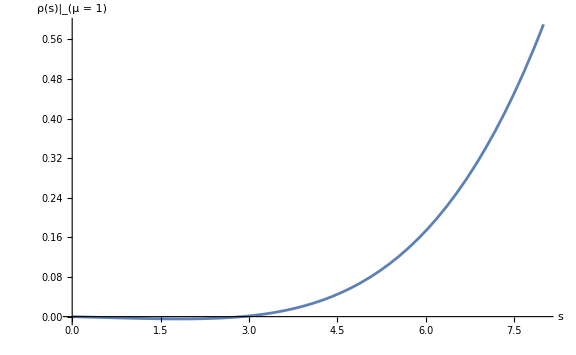
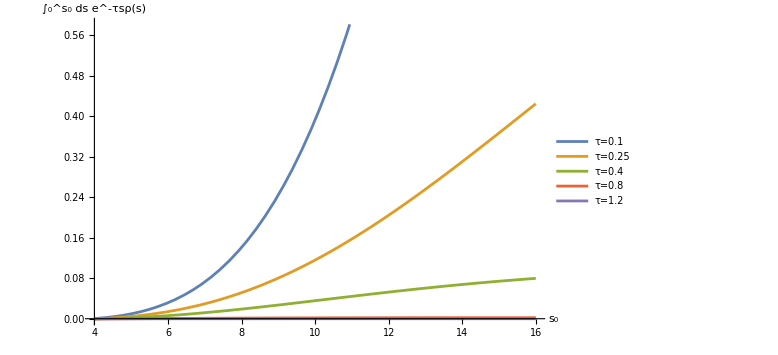

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for η_6=η_8=η_10=1

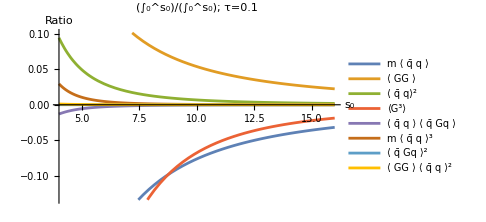
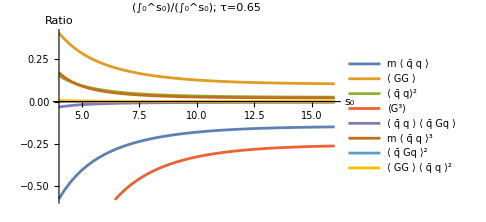
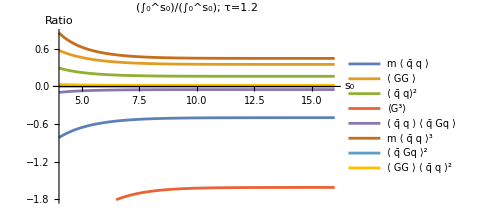

```mathematica
(*-------------------------------*)
```

ℛ^0 for η_6=η_8=η_10=1

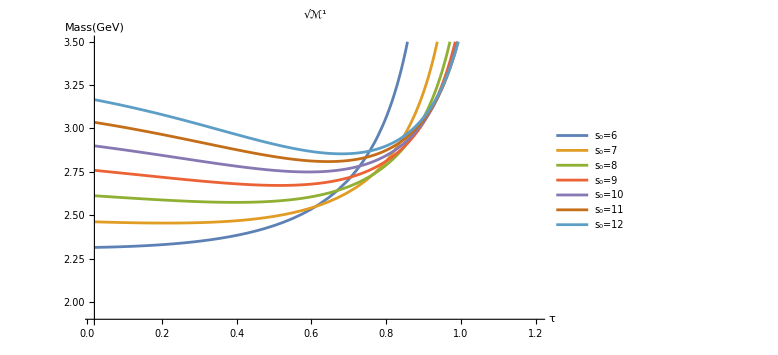
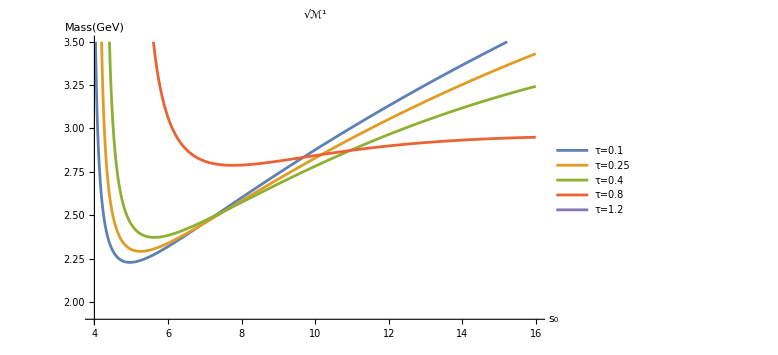

```mathematica
(*-------------------------------*)
```

ℛ^1 for η_6=η_8=η_10=1

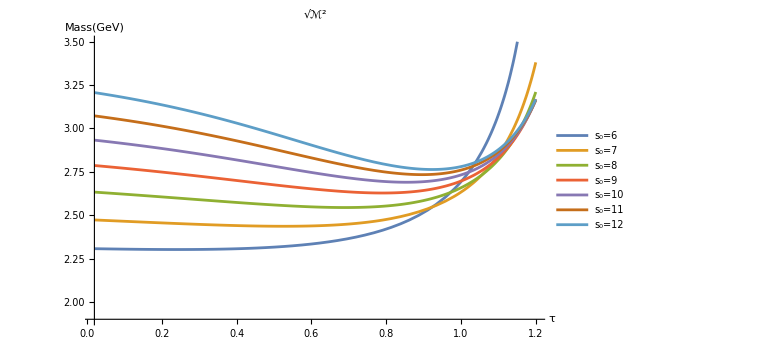
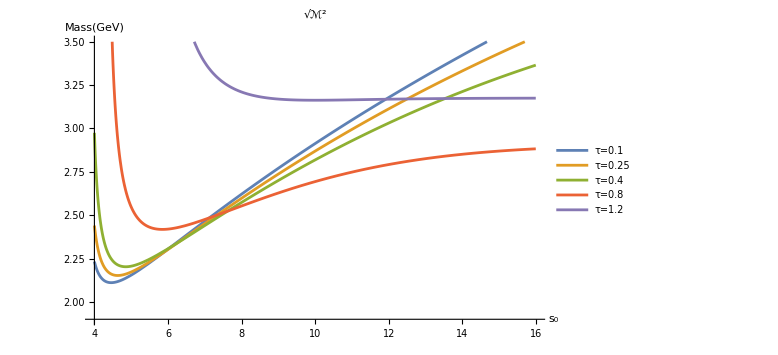

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for η_6=3, η_8=5, η_10=5

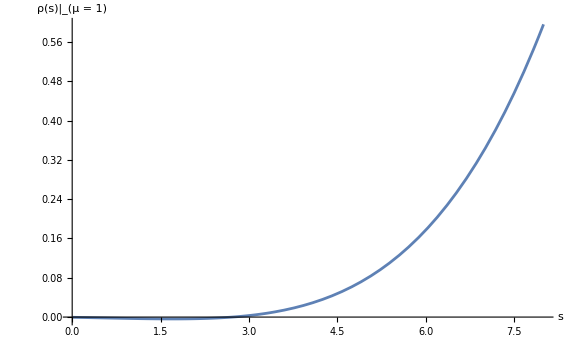
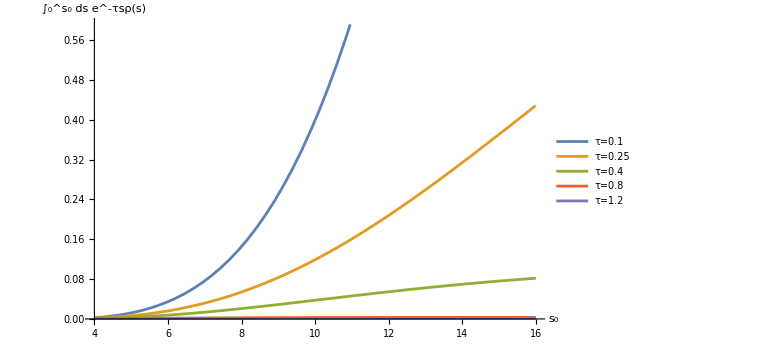

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for η_6=3, η_8=5, η_10=5

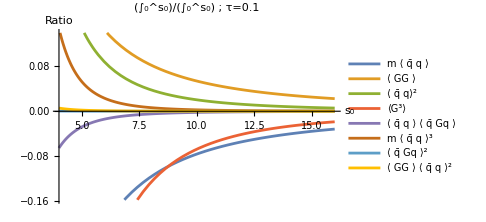
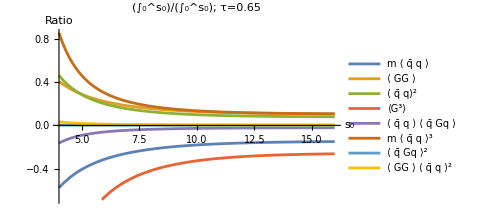
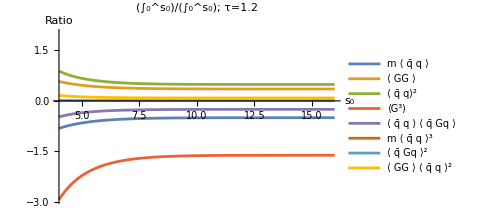

```mathematica
(*-------------------------------*)
```

ℛ^0 for η_6=3, η_8=5, η_10=5

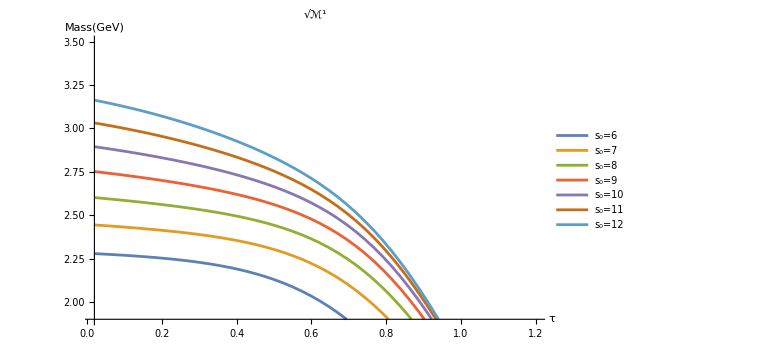
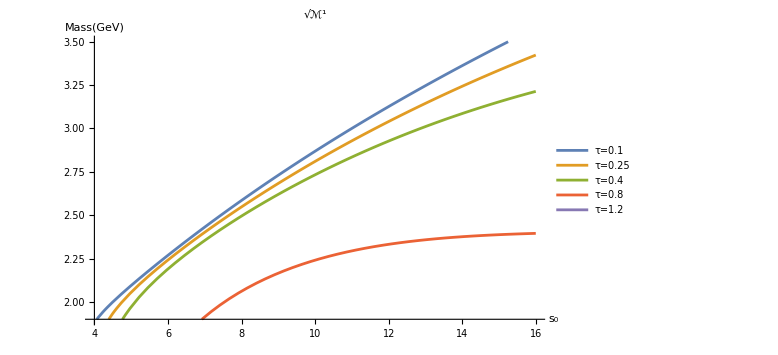

```mathematica
(*-------------------------------*)
```

ℛ^1 for η_6=3, η_8=5, η_10=5